```mathematica
ClearAll["Global`*"]
$Assumptions=A∈Integers&&A>2&&α∈Reals&&α>0&&λ∈Reals&&λ>=0&&β∈Reals&&β>0&&R∈Reals&&Rp∈Reals&&a∈Reals&&a>0&&lam∈Reals&&lam>0;
```

system parameter:
A (int) : total number of particles
F (int) : number of fragments
Z (int array) : number of particles in fragments
d (int) : number of spatial dimensions (ECCE: do not use; from the 1-dim result, one should be able to deduce the d-dim variant)

```mathematica
spacedim=3;
A=4;
F=2;
Z={A/2,A/2};
If[Total[Z]!=A||Dimensions[Z][[1]]!=F,Print["System definition erroneous."]]
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1]... Subscript[B, Subscript[Z, 1]]... Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
idPairs=Table[{n,n+Z[[1]]},{n,Z[[1]]}];
(* (B Subscript[(oson), 1] Subscript[B, 2]... Subscript[B, Subscript[Z, 1]])-(Subscript[B, 1] Subscript[B, 2].Subscript[B, Subscript[Z, 1]+Subscript[Z, 2]]) *)
(*idPairs={{1,Z[[1]]+1}}*)
(*idPairs={};*)

FrgExpWidthsR=Array[Subscript["α^r", ##]&,{F}];
FrgExpWidthsL=Array[Subscript["α^l", ##]&,{F}];

intPairs=Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}];
intBosePairs=Complement[intPairs,idPairs];
intTriples=Union[Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[2]]≠#[[3]]&],Tuples[{Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]}],Table[n,{n,Z[[1]]+1,Z[[1]]+Z[[2]]}]}]//Select[#[[1]]≠#[[2]]&]];
intBoseTriples={};
Do[
addtriple=True;
Do[
If[SubsetQ[tri,pai],addtriple=False,0]
,{pai,idPairs}];
If[addtriple,AppendTo[intBoseTriples,tri]];
,{tri,intTriples}];
intBoseTriples=DeleteDuplicates[Table[Sort[intBoseTriples[[n]]],{n,Length[intBoseTriples]}]];
Print["F_1 ⊕ F_2 = "<>ToString[Z[[1]]]<>" ⊕ "<>ToString[Z[[2]]]]
Print["Inter-cluster interaction:\n","∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = "<>ToString[Length[intBosePairs]]<>"·δ_ij + "<>ToString[Length[intBoseTriples]]<>"·δ_ijδ_ik"]
Print["Pairs = ",intBosePairs,"   Triples = ",intBoseTriples]
intPart=Join[Table[AppendTo[intBosePairs[[n]],intBosePairs[[n]][[1]]],{n,Length[intBosePairs]}],intBoseTriples,{{1,1,1}}];
```

F_1 ⊕ F_2 = 2 ⊕ 2

Inter-cluster interaction:
∑_(ij ∈ Pairs) δ_ij  +  ∑_(ijk ∈ Triples) δ_ijδ_ik = 2·δ_ij + 0·δ_ijδ_ik

Pairs = {{1,4},{2,3}}   Triples = {}

coordinate transformations:
single-particle   →  cluster-relative : T
cluster-relative  →  single-particle  : T^-1

```mathematica
SingleToCluster={};
For[f=1,f≤F,f++,{
For[i=1,i≤Z[[f]]-1,i++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+1]],0,j==Prepend[Accumulate[Z],0][[f]]+i,(Z[[f]]-1)/Z[[f]],1==1,-1/Z[[f]]],{j,1,A}]
]
}];
}];
For[f=1,f<F,f++,{
AppendTo[SingleToCluster,
Table[Which[j<=Prepend[Accumulate[Z],0][[f]],0,j>Prepend[Accumulate[Z],0][[f+2]],0,j<=Prepend[Accumulate[Z],0][[f+1]],1/Z[[f]],1==1,-1/Z[[f+1]]],{j,1,A}]
]
}];
AppendTo[SingleToCluster,
Table[1/A,{j,1,A}]
];
Single=Array[Subscript["r⃗", ##]&,{A}];
Cluster=Flatten[Table[Array[Subscript["r̄", Prepend[Accumulate[Z],0][[f]]+##]&,{Z[[f]]-1}],{f,F}]];
AppendTo[Cluster,ArrayFlatten[Array[Subscript["R⃗", ##]&,{F-1}],1][[1]]];AppendTo[Cluster,"(R⃗)_cm"];
Tmat=SingleToCluster;
Tmatinv=Inverse[SingleToCluster];
TproR=Table[If[(m==A-1),Tmat[[m,n]],0],{m,A},{n,A}];
Print[Cluster//MatrixForm,"=",SingleToCluster//MatrixForm,"·",Single//MatrixForm]
Print[Cluster//MatrixForm,"=",TproR//MatrixForm,"·",Single//MatrixForm]
```

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(1/2 | -1/2 | 0 | 0
0 | 0 | 1/2 | -1/2
1/2 | 1/2 | -1/2 | -1/2
1/4 | 1/4 | 1/4 | 1/4)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

((r̄)_1
(r̄)_3
(R⃗)_1
(R⃗)_cm)=(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1/2 | 1/2 | -1/2 | -1/2
0 | 0 | 0 | 0)·((r⃗)_1
(r⃗)_2
(r⃗)_3
(r⃗)_4)

quadratic form of fragment wave functions in cluster-relative coordinates:
ϕ_A ϕ_B=e^(-α_1(2 ∑_(j=1)^(A_1-1) r_j^2+∑_(j≠k)^(A_1-1) r_j r_k))·e^(1↔2)=∏_(i∈{1,2}) e^(-1/2(r_1,…,r_(A_i-1))(4 α_i
2 α_i
2 α_i2 α_i
4 α_i
2 α_i2 α_i
2 α_i
4 α_i) (r_1
⋮
r_(A_i-1)))
the matrix is set up row-wise
in the i-th row, the quadratic form of the j-th fragment is placed
with i-1 being the number of fragments with n<j which contain more than a single particle

```mathematica
Wmat={};
posInW=0;
For[f=1,f≤F,f++,(
If[Z[[f]]>1,
posInW+=1;
AppendTo[Wmat,Table[If[pos==posInW,Table[If[m==n,4 FrgExpWidthsR[[pos]],2 FrgExpWidthsR[[pos]]],{n,Z[[f]]-1},{m,Z[[f]]-1}],0],{pos,F}]];
];
)];
Wmat=Table[If[(m>A-2)||(n>A-2),0,ArrayFlatten[Wmat][[n]][[m]]],{n,A},{m,A}];
Print[Wmat//MatrixForm]
```

(4 (α^r)_1 | 0 | 0 | 0
0 | 4 (α^r)_2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

matrix representation of the permutation (single-particle coordinates):
(a | b | ... | A
p(a) | p(b) | ... | p(A))   original order
permuted order      ⇒    p(a)-th row→(⋮
a
⋮)=(□ | □ | □
□ | □ | □
□ | □ | □)·(a
⋮
A)
Pij[ i,j ] = Perm[ {{i,j},{j,i}} ]

```mathematica
Pij[i_,j_]:=Table[If[((r==i)&&(c==j))||((r==j)&&(c==i))||((r≠i)&&(c≠j)&&(c==r)),1,0],{r,1,A},{c,1,A}];

Perm[ord_]:=
Module[{},
pmat=IdentityMatrix[A];
Do[
pmat[[move[[1]],move[[1]]]]=0;
pmat[[move[[2]],move[[1]]]]=1;
,{move,ord}];
If[(Total[pmat,{1}]==ConstantArray[1,A])&&(Total[pmat,{2}]==ConstantArray[1,A]),
pmat,Print["illdefined permutation!"]]
];

interFragmentAntisymmetrizer=Flatten[Table[Join[DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],
Map[Reverse,DeleteDuplicates[Map[Sort,Select[Tuples[idPairs,n],DuplicateFreeQ[#]&]]],2],2
],{n,0,Length[idPairs]}],1];
Print["Inter-cluster anti-symmetrizer:\n (Â)_AB = ",interFragmentAntisymmetrizer];
```

Inter-cluster anti-symmetrizer:
 (Â)_AB = {{},{{1,3},{3,1}},{{2,4},{4,2}},{{1,3},{2,4},{4,2},{3,1}}}

quadratic form of a two-body Gaussian interaction in cluster-relative coordinates:
V_(F_1 F_2)=∑_((i∈F_1)_(j∈F_2)) e^(-(λ(r_i-r_j))^2)

```mathematica
Pv[i_,j_]:=Table[If[(n==m==j)||(n==m==i),1,0],{n,A},{m,A}];
Vr[i_,j_,λ_]:=If[i≠j,Table[Which[((n==m==i))||((n==m==(j))),2 λ,((n==i)&&(m==j))||((m==i)&&(n==j)),-2 λ,1==1,0],{n,A},{m,A}],Table[0,{n,A},{m,A}]];
Vij[i_,j_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv;
Vijk[i_,j_,k_,λ_]:=Transpose[Pv[i,j].Tmatinv].Vr[i,j,λ].Pv[i,j].Tmatinv+Transpose[Pv[i,k].Tmatinv].Vr[i,k,λ].Pv[i,k].Tmatinv;
```

full quadratic form of a two-body Gaussian interaction between i,j and a permutation of particles m,n (matrix representation in cluster-relative coordinates):
dimer-dimer w/o discrete scale invariance:  V=δ_13+δ_23+δ_24+δ_234+δ_123    A=OverHat[1]-P_14

```mathematica
{ivtest,jvtest,kvtest}=intPart[[-1]]
testperm={};(*{{1,4},{4,1},{2,5},{5,2},{3,6},{6,3}}*)
λ=0;
Wfull[iv_,jv_,kv_,permu_,λ_]:=Flatten[Wmat/.{FrgExpWidthsR[[#]]->FrgExpWidthsL[[#]]&/@Range[F]},1]+Vijk[iv,jv,kv,λ]+Transpose[(Tmat.Perm[permu].Tmatinv)].(Wmat).(Tmat.Perm[permu].Tmatinv);
Sfull[permu_]:=TproR.Perm[permu].Tmatinv;
Amat[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[1;;(A-2),1;;(A-2)]];
S3[Rp_,s_,iv_,jv_,kv_,permu_,λ_]:=-Rp Wfull[iv,jv,kv,permu,λ][[A-1,1;;A-2]]-I s Sfull[permu][[A-1,1;;A-2]];
S4[s_,permu_]:=-I s Sfull[permu][[A-1,A-1]];
M1[iv_,jv_,kv_,permu_,λ_]:=Wfull[iv,jv,kv,permu,λ][[A-1,A-1]];
Print["W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = ",Wfull[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (S̲)_full = T_RPT^-1 = ",Sfull[testperm]//MatrixForm,"         (V̲)_ij = ",Vij[ivtest,jvtest,λ]//MatrixForm,"         (V̲)_ijk = ",Vijk[ivtest,jvtest,kvtest,λ]//MatrixForm]
Print["         A̲ = ",Amat[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         (A̲)^-1 = ",Simplify[Inverse[Amat[ivtest,jvtest,kvtest,testperm,λ]]]//MatrixForm,"         S_3 = ",S3[Rp,s,ivtest,jvtest,kvtest,testperm,λ]//MatrixForm,"         S_4 = ",S4[s,testperm]//MatrixForm,"         M_1 = ",M1[ivtest,jvtest,kvtest,testperm,λ]//MatrixForm]
```

{1,1,1}

W̲+V̲+(TPT^-1)^TW̲(TPT^-1) = (4 (α^l)_1+4 (α^r)_1 | 0 | 0 | 0
0 | 4 (α^l)_2+4 (α^r)_2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)         (S̲)_full = T_RPT^-1 = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)         (V̲)_ij = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)         (V̲)_ijk = (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

A̲ = (4 (α^l)_1+4 (α^r)_1 | 0
0 | 4 (α^l)_2+4 (α^r)_2)         (A̲)^-1 = (1/(4 (α^l)_1+4 (α^r)_1) | 0
0 | 1/(4 (α^l)_2+4 (α^r)_2))         S_3 = (0
0)         S_4 = -ⅈ s         M_1 = 0

r̄ - integration

```mathematica
scoeff[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=CoefficientList[Simplify[1/2 S3[Rp,s,iv,jv,kv,permu,λ].Inverse[Amat[iv,jv,kv,permu,λ]].S3[Rp,s,iv,jv,kv,permu,λ]-1/2 Rp M1[iv,jv,kv,permu,λ] Rp+S4[s,permu] Rp+I s Rpp],s];
S5[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[2]]];
S6[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[1]]];
Kmat[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=
If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
-2 Simplify[scoeff[Rp,Rpp,iv,jv,kv,permu,λ][[3]]]
];
Kmatinv[Rp_,Rpp_,iv_,jv_,kv_,permu_,λ_]:=If[Length[scoeff[Rp,Rpp,iv,jv,kv,permu,λ]]<3,
0
,
1/Kmat[Rp,Rpp,iv,jv,kv,permu,λ]
];
Print[S6[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ]," + ",S5[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s  +",Kmat[Rp,Rpp,ivtest,jvtest,kvtest,testperm,λ],"s^2"]
```

0 + -ⅈ (Rp-Rpp)s  +0s^2

s - integration

(T̂-E)_direct                                                                            :  λ=0  ,  i_p=j_p                  ⇒P̂=𝟙
δ_13^X (no scale invariance (ab)-(ca) dimer-dimer)  :  λ=Λ ,  i_p=1 ,j_p=4 ⇒(P̂)_14
ECCE:  ∫d^(spacedim)(r_1,…,r_(A-2),s)ϕ_A ϕ_B δ(s)=(2π)^(spacedim/2)/((2π)^spacedim(√(det(K)))^spacedim)((2π)^(dim(W)/2)/(√(det(W_((A-2)×(A-2))))))^spacedim

```mathematica
genericRGMEQcomponent[R_,Rp_,a1_,a2_,lec_,lam_,ii_,jj_,kk_,permu_]:=Module[{λ},
kin=(lam==0);

Rcoeff=CoefficientList[
1/2 S5[R,Rp,ii,jj,kk,permu,lam] Kmatinv[R,Rp,ii,jj,kk,permu,lam] S5[R,Rp,ii,jj,kk,permu,lam]+S6[R,Rp,ii,jj,kk,permu,lam]
,Rp];

If[Length[Rcoeff]==0,αRp=αRRp=αR=0,αR=Simplify[Rcoeff[[1]]/.{α->a1,β->a2}]];
If[Length[Rcoeff]>1,αRRp=Simplify[Rcoeff[[2]]/.{α->a1,β->a2}],αRRp=0];
If[Length[Rcoeff]==3,αRp=Simplify[Rcoeff[[3]]/.{α->a1,β->a2}],αRp=0];

detA=Simplify[Det[Amat[ii,jj,kk,permu,lam]]/.{α->a1,β->a2}];
detK=If[Length[scoeff[R,Rp,ii,jj,kk,permu,lam]]<3,1,Simplify[Kmat[R,Rp,ii,jj,kk,permu,lam]/.{α->a1,β->a2}]];

strength=lec (Simplify[1/(2 Pi) (2 Pi)^((A-2)/2)/Sqrt[detA] (2 Pi)^(1/2)/Sqrt[detK]])^spacedim;

Simplify[strength Exp[Simplify[αR+αRp Rp^2+αRRp Rp]]]
];
```

```mathematica
a=α;b=β;
LEC=1;
lamba=0;
ivtest=2;jvtest=4;kvtest=2;
normierung=genericRGMEQcomponent["r","r̃",a,b,LEC,lamba,ivtest,jvtest,kvtest,{}];
Print["Norm = ∫ϕ_Aϕ_B = ",normierung]
```

Norm = ∫ϕ_Aϕ_B = π^(3/2)/(16 √2 (((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))^(3/2))

## Aimer-Bimer (B_1 B_2... B_Z_1) - (B_(Z_1+1)... B_(Z_1+Z_2)) (scale variant with(out) 3-body forces)

ECCE: interacting pairs and triplets, and the elements of the inter-cluster antisymmetrizer are set
at the beginning of this notebook

```mathematica
permu=interFragmentAntisymmetrizer[[-1]]
ijk=intPart[[-1]];
coef="OverHat[(T]-E)";
range=0;
Print["interacting particles: ",ijk];
Simplify[genericRGMEQcomponent[x,y,α,β,coef,range,ijk[[1]],ijk[[2]],ijk[[3]],permu](*/normierung*)]
```

{{1,3},{2,4},{4,2},{3,1}}

interacting particles: {1,1,1}

(OverHat[(T]-E) π^(3/2))/(16 √2 (((α^l)_2+(α^r)_1) ((α^l)_1+(α^r)_2))^(3/2))

```mathematica
SetSharedVariable[RGMequationComponents]
RGMequationComponents={};
Clear[i]
Do[
WWcoef={"D_1","C_0","(T̂-E)"}[[Max[Counts[ijk]]]];
WWrange={Λ,Λ,0}[[Max[Counts[ijk]]]];
ParallelDo[
signpermut=(-1)^(Length[permu]/2);
AppendTo[RGMequationComponents,Simplify[signpermut genericRGMEQcomponent[x,y,α,β,WWcoef,WWrange,ijk[[1]],ijk[[2]],ijk[[3]],permu]]];
,{permu,interFragmentAntisymmetrizer}]
,{ijk,intPart}]
```

```mathematica
TableForm[(*1/(normierung)*) Simplify[RGMequationComponents],TableSpacing->{5,5}]
```

(C_0 ⅇ^(-(2 x^2 Λ ((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))/(Λ (α^r)_1+(α^l)_2 (Λ+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_2))) π^(3/2))/(8 (Λ (α^r)_1+(α^l)_2 (Λ+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_2))^(3/2))
(C_0 ⅇ^(-(2 x^2 Λ ((α^l)_2+(α^r)_1) ((α^l)_1+(α^r)_2))/(Λ (α^r)_1+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_2 (Λ+2 (α^r)_2))) π^(3/2))/(8 (Λ (α^r)_1+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_2 (Λ+2 (α^r)_2))^(3/2))
-(C_0 ⅇ^(-(4 x^2 (α^r)_1 (2 Λ+(α^r)_2)+(α^l)_2 ((x+y)^2 (α^r)_1+(x-y)^2 (2 Λ+(α^r)_2))+(α^l)_1 (4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+(x+y)^2 (2 Λ+(α^r)_2)))/(2 (2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(2 √2 ((2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))
-(C_0 ⅇ^(-(4 x^2 (2 Λ+(α^r)_1) (α^r)_2+(α^l)_2 (2 (x+y)^2 Λ+(x+y)^2 (α^r)_1+(x-y)^2 (α^r)_2)+(α^l)_1 (2 x^2 Λ-4 x y Λ+2 y^2 Λ+4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+x^2 (α^r)_2+2 x y (α^r)_2+y^2 (α^r)_2))/(2 (2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(2 √2 ((2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))
(C_0 ⅇ^(-(2 x^2 Λ ((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))/(Λ (α^r)_1+(α^l)_2 (Λ+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_2))) π^(3/2))/(8 (Λ (α^r)_1+(α^l)_2 (Λ+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_2))^(3/2))
(C_0 ⅇ^(-(2 x^2 Λ ((α^l)_2+(α^r)_1) ((α^l)_1+(α^r)_2))/(Λ (α^r)_1+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_2 (Λ+2 (α^r)_2))) π^(3/2))/(8 (Λ (α^r)_1+(α^l)_1 (Λ+2 (α^l)_2+2 (α^r)_1)+Λ (α^r)_2+2 (α^r)_1 (α^r)_2+(α^l)_2 (Λ+2 (α^r)_2))^(3/2))
-(C_0 ⅇ^(-(4 x^2 (2 Λ+(α^r)_1) (α^r)_2+(α^l)_2 (2 (x+y)^2 Λ+(x+y)^2 (α^r)_1+(x-y)^2 (α^r)_2)+(α^l)_1 (2 x^2 Λ-4 x y Λ+2 y^2 Λ+4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+x^2 (α^r)_2+2 x y (α^r)_2+y^2 (α^r)_2))/(2 (2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(2 √2 ((2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))
-(C_0 ⅇ^(-(4 x^2 (α^r)_1 (2 Λ+(α^r)_2)+(α^l)_2 ((x+y)^2 (α^r)_1+(x-y)^2 (2 Λ+(α^r)_2))+(α^l)_1 (4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+(x+y)^2 (2 Λ+(α^r)_2)))/(2 (2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(2 √2 ((2 Λ+(α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 (2 Λ+(α^r)_1+(α^r)_2)+(α^l)_1 (2 Λ+4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))
((T̂-E) π^(3/2))/(16 √2 (((α^l)_1+(α^r)_1) ((α^l)_2+(α^r)_2))^(3/2))
((T̂-E) π^(3/2))/(16 √2 (((α^l)_2+(α^r)_1) ((α^l)_1+(α^r)_2))^(3/2))
-((T̂-E) ⅇ^(-(4 x^2 (α^r)_1 (α^r)_2+(α^l)_2 ((x+y)^2 (α^r)_1+(x-y)^2 (α^r)_2)+(α^l)_1 (4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+(x+y)^2 (α^r)_2))/(2 ((α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(2 √2 (((α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 ((α^r)_1+(α^r)_2)+(α^l)_1 (4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 ((α^r)_1+(α^r)_2)+(α^l)_1 (4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))
-((T̂-E) ⅇ^(-(4 x^2 (α^r)_1 (α^r)_2+(α^l)_2 ((x+y)^2 (α^r)_1+(x-y)^2 (α^r)_2)+(α^l)_1 (4 y^2 (α^l)_2+(x-y)^2 (α^r)_1+(x+y)^2 (α^r)_2))/(2 ((α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2))) π^(3/2))/(2 √2 (((α^l)_1+(α^l)_2+(α^r)_1+(α^r)_2)/((α^l)_2 ((α^r)_1+(α^r)_2)+(α^l)_1 (4 (α^l)_2+(α^r)_1+(α^r)_2)))^(3/2) ((α^l)_2 ((α^r)_1+(α^r)_2)+(α^l)_1 (4 (α^l)_2+(α^r)_1+(α^r)_2))^(3/2))

ℵ) first isolate the summands which correspond to the kinetic energy and insert the derivatives and the ℏ...
ℶ) add the rest and be careful about the sign of the E term
ℷ) add up all components except for the remaining  (-ℏ^2/(2μ)∂_r^2 +E)

(ab)-(cd) dimer-dimer potential

```mathematica
Length[RGMequationComponents]
RGMequationComponents[[577]]
```

592

((T̂-E) π^(15/2))/(128 √2 ((α+β)^6)^(3/2))

```mathematica
(*1/normierung*) (*Total[RGMequationComponents]*)
(*ExchangeKernel[r_,rp_,alphai_,alphaj_,En_,hbc2m_]:=(*1/(normierung)*) ( -"ℏ^2/(2 μ)·"(D[(Total[RGMequationComponents[[-16;;]]]/."(T̂-E)"->1),{x,2}])-(Total[RGMequationComponents[[-16;;]]]/."(T̂-E)"->"E"))/.{x->r,y->rp,α->alphai,β->alphaj,"E"->En,"ℏ^2/(2 μ)·"->hbc2m};*)
(*ExchangePotential[r_,rp_,alphai_,alphaj_,lambda_,c0_,d0_]:=(*1/(normierung)*) Total[RGMequationComponents[[;;576]]]/.{x->r,y->rp,α->alphai,β->alphaj,Λ->lambda,"C_0"->c0,"D_1"->d0};*)
ExchangePotentialC[r_,rp_,alphai_,alphaj_,lambda_,c0_,d0_]:=(*1/(normierung)*) Total[RGMequationComponents[[;;192]]]/.{x->r,y->rp,α->alphai,β->alphaj,Λ->lambda,"C_0"->c0,"D_1"->d0};
(*ExchangePotentialD[r_,rp_,alphai_,alphaj_,lambda_,c0_,d0_]:=(*1/(normierung)*) Total[RGMequationComponents[[193;;576]]]/.{x->r,y->rp,α->alphai,β->alphaj,Λ->lambda,"C_0"->c0,"D_1"->d0};*)
Simplify[ExchangePotentialC["R","Rp","α","α","λ","C","D"]]
(*Simplify[ExchangePotentialD["R","Rp","α","α","λ","C","D"]]*)
```

(3 C ((√2 ⅇ^(-(4 R^2 α λ)/(4 α+3 λ)))/((α^5 (4 α+3 λ))^(3/2))+(4 √2 ⅇ^(-(4 α (-R Rp λ+R^2 (α+λ)+Rp^2 (α+λ)))/(2 α+λ)))/((α^5 (α+λ))^(3/2) ((2 α+λ)/(α^2+α λ))^(3/2))+(4 √2 ⅇ^(-(4 α (R Rp λ+R^2 (α+λ)+Rp^2 (α+λ)))/(2 α+λ)))/((α^5 (α+λ))^(3/2) ((2 α+λ)/(α^2+α λ))^(3/2))-(32 ⅇ^(-(2 α (-4 R Rp (2 α+λ)+R^2 (5 α+4 λ)+Rp^2 (5 α+4 λ)))/(3 α+2 λ)))/((α^5 (5 α+4 λ))^(3/2) ((3 α+2 λ)/(5 α^2+4 α λ))^(3/2))-(32 ⅇ^(-(2 α (4 R Rp (2 α+λ)+R^2 (5 α+4 λ)+Rp^2 (5 α+4 λ)))/(3 α+2 λ)))/((α^5 (5 α+4 λ))^(3/2) ((3 α+2 λ)/(5 α^2+4 α λ))^(3/2))+(64 ⅇ^(-2 α (Rp^2+(R^2 (4 α+5 λ))/(4 α+3 λ))))/((1/α)^(3/2) (α^5 (4 α+3 λ))^(3/2))-(32 ⅇ^(-(2 α (-8 R Rp (α+λ)+Rp^2 (5 α+4 λ)+R^2 (5 α+6 λ)))/(3 α+2 λ)))/((α^5 (5 α+4 λ))^(3/2) ((3 α+2 λ)/(5 α^2+4 α λ))^(3/2))-(32 ⅇ^(-(2 α (8 R Rp (α+λ)+Rp^2 (5 α+4 λ)+R^2 (5 α+6 λ)))/(3 α+2 λ)))/((α^5 (5 α+4 λ))^(3/2) ((3 α+2 λ)/(5 α^2+4 α λ))^(3/2))) π^(15/2))/2048

```mathematica
Clear[λ];
Simplify[ExchangePotential["R","Rp","α","α","λ","C","D"]]
```

$Aborted

```mathematica
Simplify[ExchangeKernel["R","Rp",α,β,"Ε","ℏ^2/(2  μ)"]]
```

$Aborted

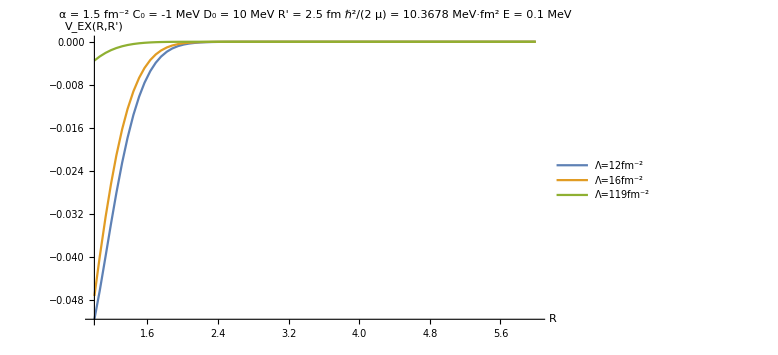
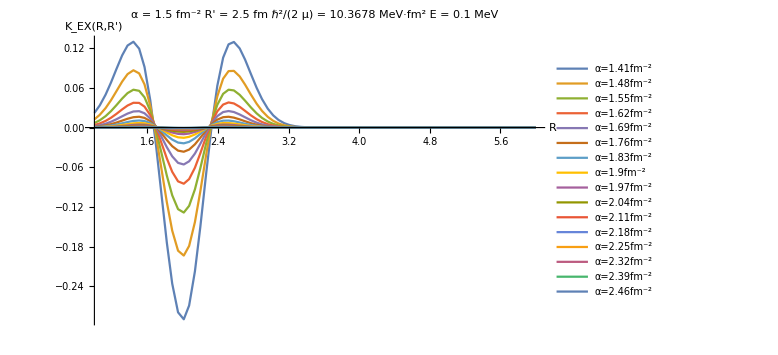
-Graphics- | -Graphics-

```mathematica
ℏc=197.32858;Mnucl=(938.2796+939.5731)/2.;
mu=Mnucl Z[[1]] Z[[2]]/(Z[[1]]+Z[[2]]);
hbc2m=ℏc^2/(2 mu);

Rmax=6.0;y0=2.5;alpha=1.5;c0=-1;d0=10;en=0.10;lambdas={12,16,119};alphas=Table[0.01+n 0.07,{n,20,35}];

Grid[{{
Plot[Evaluate@Table[ExchangePotential[r,y0,alpha,lambda,c0,d0],{lambda,lambdas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","V_EX(R,R')"},PlotLegends->Table["Λ="<>ToString[n]<>"fm^-2",{n,lambdas}],PlotRange->Full,ImageSize->Large,PlotLabel->"α = "<>ToString[alpha]<>" fm^-2   C_0 = "<>ToString[c0]<>" MeV    D_0 = "<>ToString[d0]<>" MeV    R' = "<>ToString[y0]<>" fm    ℏ^2/(2  μ) = "<>ToString[hbc2m]<>" MeV·fm^2     E = "<>ToString[en]<>" MeV"],
Plot[Evaluate@Table[ExchangeKernel[r,y0,alpha,en,hbc2m],{alpha,alphas}],{r,1,Rmax},PlotPoints->80,MaxRecursion->0,AxesLabel->{"R","K_EX(R,R')"},PlotLegends->Table["α="<>ToString[n]<>"fm^-2",{n,alphas}],PlotRange->Full,ImageSize->Large,PlotLabel->"α = "<>ToString[alpha]<>" fm^-2    R' = "<>ToString[y0]<>" fm    ℏ^2/(2  μ) = "<>ToString[hbc2m]<>" MeV·fm^2     E = "<>ToString[en]<>" MeV"]
}}]
```

```mathematica
bet=3;gam=1;
exponent=Function[{r,rp,alpha,beta,gamma},Exp[-alpha r^2-gamma rp^2] Cosh[beta r rp]];
Animate[Plot3D[exponent[r,rp,alf,bet,gam],{r,-3,3},{rp,-3,3},PlotRange->Full],{alf,1.1,10,0.1},AnimationRunning->False]
```

```mathematica
ThreeJSymbol[{1,0},{0,0},{1,0}]
SphericalBesselJ[3,0]
```

-1/(√3)

0

```mathematica
Clear[a,lam,c,d,e]
terme=Table[1/(2 normierung) RGMequationComponents[[m]]/.{x->r,y->rp,α->a,Λ->lam,"C_0"->c,"D_1"->d,"E"->e,"-ℏ^2/(2  μ)·"->hbc2m},{m,1,Length[RGMequationComponents]-16}];
termekin=Table[1/(2 normierung) RGMequationComponents[[m]]/.{x->r,y->rp,α->a,Λ->lam,"C_0"->c,"D_1"->d,"E"->e,"-ℏ^2/(2  μ)·"->hbc2m},{m,Length[RGMequationComponents]-16+1,Length[RGMequationComponents]}];
```

```mathematica
Simplify[Total[termekin]]
```

(T̂-E)+1/9 (T̂-E) a^(3/2) (432 √2 ⅇ^(-2 a (r^2+rp^2))-256 √6 ⅇ^(-2/3 a (5 r^2-8 r rp+5 rp^2))-256 √6 ⅇ^(-2/3 a (5 r^2+8 r rp+5 rp^2)))

```mathematica
termeLargeL=Table[Normal[Series[Coefficient[terme[[mm]]/.Exponent[terme[[mm]],E]->n,E^n],{a,0,5}]] Exp[Limit[Exponent[terme[[mm]],E],lam->Infinity]],{mm,1,Length[terme]}];
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

General::stop: Further output of Limit::alimv will be suppressed during this calculation.

```mathematica
Total[termeLargeL]
```

24 ⅇ^(-2 a r^2) ((639 a^5 d)/(16 √2 lam^5)-(21 a^4 d)/(2 √2 lam^4)+(√2 a^3 d)/lam^3)+24 ⅇ^(-2 a r^2) ((111 a^5 d)/(4 √2 lam^5)-(9 a^4 d)/(√2 lam^4)+(√2 a^3 d)/lam^3)+24 ⅇ^(-(4 a r^2)/3) (-(560 a^(9/2) c)/(81 √3 lam^(9/2))+(40 a^(7/2) c)/(9 √3 lam^(7/2))-(8 a^(5/2) c)/(3 √3 lam^(5/2))+(4 a^(3/2) c)/(3 √3 lam^(3/2)))+24 ⅇ^(-4 a (r^2-r rp+rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+24 ⅇ^(-4 a (r^2+r rp+rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+24 ⅇ^(-2 a (3 r^2-4 r rp+2 rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+24 ⅇ^(-2 a (3 r^2+4 r rp+2 rp^2)) (-(135 a^5 c)/lam^(7/2)+(72 a^4 c)/lam^(5/2)-(32 a^3 c)/lam^(3/2))+12 ⅇ^(-4 a (r^2-r rp+rp^2)) ((240 a^5 c)/lam^(7/2)-(96 a^4 c)/lam^(5/2)+(32 a^3 c)/lam^(3/2))+12 ⅇ^(-4 a (r^2+r rp+rp^2)) ((240 a^5 c)/lam^(7/2)-(96 a^4 c)/lam^(5/2)+(32 a^3 c)/lam^(3/2))+48 ⅇ^(-2/3 a (5 r^2+3 rp^2)) ((640 √(2/3) a^5 c)/(9 lam^(7/2))-(128 √(2/3) a^4 c)/(3 lam^(5/2))+(64 √(2/3) a^3 c)/(3 lam^(3/2)))+(1536 a^(9/2) d ⅇ^(-2 a (2 r^2+rp^2)))/lam^3-(3072 √2 a^(9/2) d ⅇ^(-2 a (3 r^2-4 r rp+3 rp^2)))/lam^3-(3072 √2 a^(9/2) d ⅇ^(-2 a (3 r^2+4 r rp+3 rp^2)))/lam^3-(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (19 r^2-24 r rp+11 rp^2)))/(5 lam^3)+(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (11 r^2-8 r rp+11 rp^2)))/(5 lam^3)+(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (11 r^2+8 r rp+11 rp^2)))/(5 lam^3)-(12288 √(2/5) a^(9/2) d ⅇ^(-2/5 a (19 r^2+24 r rp+11 rp^2)))/(5 lam^3)

```mathematica
Simplify[%]
```

12/25 ((3200 a^(9/2) d ⅇ^(-2 a (2 r^2+rp^2)))/lam^3-(6400 √2 a^(9/2) d ⅇ^(-2 a (3 r^2-4 r rp+3 rp^2)))/lam^3-(6400 √2 a^(9/2) d ⅇ^(-2 a (3 r^2+4 r rp+3 rp^2)))/lam^3-(1024 √10 a^(9/2) d ⅇ^(-2/5 a (19 r^2-24 r rp+11 rp^2)))/lam^3+(1024 √10 a^(9/2) d ⅇ^(-2/5 a (11 r^2-8 r rp+11 rp^2)))/lam^3+(1024 √10 a^(9/2) d ⅇ^(-2/5 a (11 r^2+8 r rp+11 rp^2)))/lam^3-(1024 √10 a^(9/2) d ⅇ^(-2/5 a (19 r^2+24 r rp+11 rp^2)))/lam^3+(400 a^3 c ⅇ^(-4 a (r^2-r rp+rp^2)) (15 a^2-6 a lam+2 lam^2))/lam^(7/2)+(400 a^3 c ⅇ^(-4 a (r^2+r rp+rp^2)) (15 a^2-6 a lam+2 lam^2))/lam^(7/2)+(6400 √(2/3) a^3 c ⅇ^(-2/3 a (5 r^2+3 rp^2)) (10 a^2-6 a lam+3 lam^2))/(9 lam^(7/2))+(25 a^3 d ⅇ^(-2 a r^2) (111 a^2-36 a lam+8 lam^2))/(2 √2 lam^5)+(25 a^3 d ⅇ^(-2 a r^2) (639 a^2-168 a lam+32 lam^2))/(8 √2 lam^5)-(50 a^3 c ⅇ^(-4 a (r^2-r rp+rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)-(50 a^3 c ⅇ^(-4 a (r^2+r rp+rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)-(50 a^3 c ⅇ^(-2 a (3 r^2-4 r rp+2 rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)-(50 a^3 c ⅇ^(-2 a (3 r^2+4 r rp+2 rp^2)) (135 a^2-72 a lam+32 lam^2))/lam^(7/2)+(200 a^(3/2) c ⅇ^(-(4 a r^2)/3) (-140 a^3+90 a^2 lam-54 a lam^2+27 lam^3))/(81 √3 lam^(9/2)))